```mathematica
h=Table[allGraphs5[k,"colofourrealnull"],{k,Select[allGraphs5NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs5[#,"colofourrealnull"],4]]]≠1&]}]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n124x3x5,n12x34x5,n13x2x4x5,n134x2x5,n13x24x5,n14x2x3x5,n14x23x5,n1x23x4x5,n1x234x5,n1x24x3x5,n1x2x34x5}

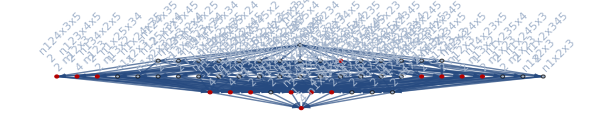

```mathematica
With[
{h=Table[allGraphs5[k,"colofourrealnull"],{k,Select[allGraphs5NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs5[#,"colofourrealnull"],4]]]≠1&]}]},
Graph[MobiusGraph4[k5Key,allGraphs5],GraphHighlight->h]
]
```

```mathematica
def=Map[allGraphs4[#,"colofourrealnull"]&,Select[allGraphs4NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs4[#,"colofourrealnull"],3]]]≠1&]]
```

{n1x2x3x4,n12x3x4,n123x4,n13x2x4,n1x23x4}

```mathematica
Map[allGraphs4[#,"colofourrealnull"]&,Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofourrealnull"]]]==5&&Length[Intersection[ListofVars[allGraphs4[#,"colofourrealnull"]],def]]==5&]]
```

{2 n123x4-n12x3x4-n13x2x4-n1x23x4+n1x2x3x4}

```mathematica
Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofourrealnull"]]]==5&&Length[Intersection[ListofVars[allGraphs4[#,"colofourrealnull"]],def]]==5&]
```

{333}

```mathematica
allGraphs4[333,"graph"]
```

-Graphics-

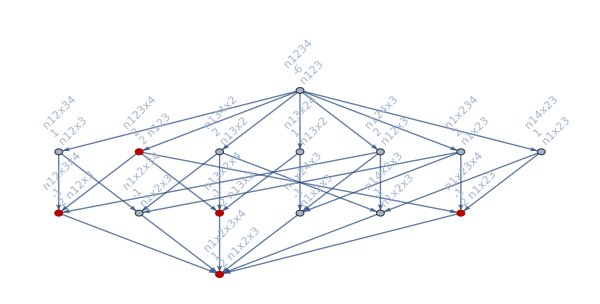

```mathematica
With[
{h=Table[allGraphs4[k,"colofourrealnull"],{k,Select[allGraphs4NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs4[#,"colofourrealnull"],3]]]≠1&]}]},
Graph[MobiusGraph4[K4Key,allGraphs4],GraphHighlight->h]
]
```

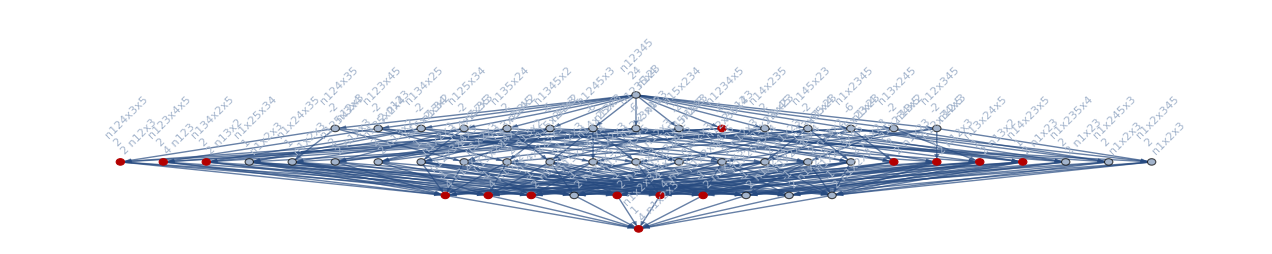

```mathematica
With[
{h=Table[allGraphs5[k,"colofourrealnull"],{k,Select[allGraphs5NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs5[#,"colofourrealnull"],4]]]≠1&]}]},
Graph[MobiusGraph4[k5Key,allGraphs5],GraphHighlight->h]
]
```

```mathematica
With[
{h=Table[allGraphs6[k,"colofourrealnull"],{k,Select[allGraphs6NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs6[#,"colofourrealnull"],5]]]≠1&]}]},
Graph[MobiusGraph4[K6Key,allGraphs6],GraphHighlight->h]
]
```

$Aborted

```mathematica
def2=Map[allGraphs5[#,"colofourrealnull"]&,Select[allGraphs5NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs5[#,"colofourrealnull"],4]]]≠1&]]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n124x3x5,n12x34x5,n13x2x4x5,n134x2x5,n13x24x5,n14x2x3x5,n14x23x5,n1x23x4x5,n1x234x5,n1x24x3x5,n1x2x34x5}

```mathematica
Length[def2]
```

15

```mathematica
Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourrealnull"]]]==15&&Length[Intersection[ListofVars[allGraphs5[#,"colofourrealnull"]],def2]]==15&]
```

{28764}

```mathematica
allGraphs5[28764,"graph"]
```

-Graphics-

```mathematica
def3=Map[allGraphs6[#,"colofourrealnull"]&,Select[allGraphs6NullAtomKeys,First[FactorTermsList[ DropMore[allGraphs6[#,"colofourrealnull"],5]]]≠1&]]
```

{n1x2x3x4x5x6,n12x3x4x5x6,n123x4x5x6,n1234x5x6,n12345x6,n1235x4x6,n123x45x6,n124x3x5x6,n1245x3x6,n124x35x6,n125x3x4x6,n125x34x6,n12x34x5x6,n12x345x6,n12x35x4x6,n12x3x45x6,n13x2x4x5x6,n134x2x5x6,n1345x2x6,n134x25x6,n135x2x4x6,n135x24x6,n13x24x5x6,n13x245x6,n13x25x4x6,n13x2x45x6,n14x2x3x5x6,n145x2x3x6,n145x23x6,n14x23x5x6,n14x235x6,n14x25x3x6,n14x2x35x6,n15x2x3x4x6,n15x23x4x6,n15x234x6,n15x24x3x6,n15x2x34x6,n1x23x4x5x6,n1x234x5x6,n1x2345x6,n1x235x4x6,n1x23x45x6,n1x24x3x5x6,n1x245x3x6,n1x24x35x6,n1x25x3x4x6,n1x25x34x6,n1x2x34x5x6,n1x2x345x6,n1x2x35x4x6,n1x2x3x45x6}

```mathematica
Length[def3]
```

52

```mathematica
Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,"colofourrealnull"]]]==52&&Length[Intersection[ListofVars[allGraphs6[#,"colofourrealnull"]],def3]]==52&]
```

{7114644}

```mathematica
allGraphs6[7114644,"graph"]
```

-Graphics-